```mathematica
(* AnalyticSignalFromWav.nb *)
(* created at 2015-06-21 *)
```

```mathematica
wav=-Graphics-;
```

```mathematica
step[n_Integer?Positive]:=1+Sign[Sin[π Range[1,-1,-2/n]//Most]]
wind[li_List]:=InverseFourier[Fourier[li]*step[Length[li]]]
```

```mathematica
li=wav⟦1⟧⟦1⟧⟦1⟧;
len=li//Length
compli=wind[li];
```

133182

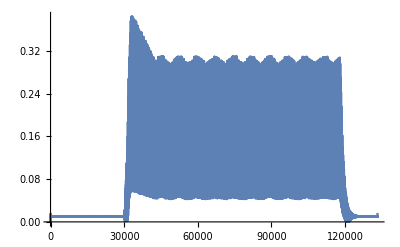

```mathematica
ListLinePlot[Abs[compli],PlotRange->{All,All}]
```

{60000,61000}

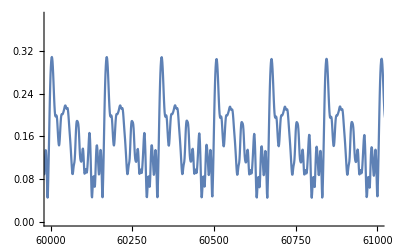

```mathematica
mainrange={60000,61000}
ListLinePlot[Abs[compli],PlotRange->{mainrange,All}]
```

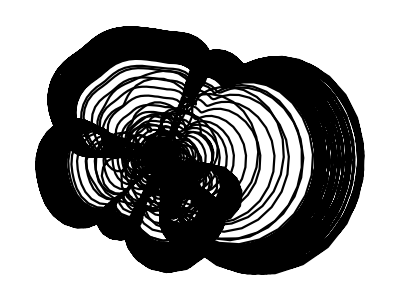

```mathematica
ListLinePlot[{Im[compli],Re[compli]}ᵀ,PlotRange->All,AspectRatio->Automatic,Axes->False,PlotStyle->Black]
```

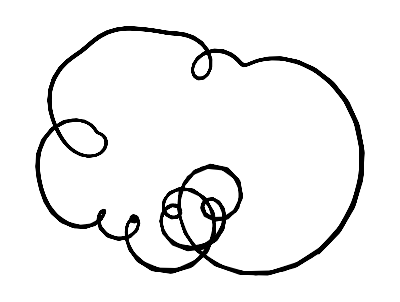

```mathematica
ListLinePlot[Take[{Im[compli],Re[compli]}ᵀ,mainrange],PlotRange->All,AspectRatio->Automatic,Axes->None,PlotStyle->Black]
```